((3 p^2-2 p^3)^2)/(1-(1-p)^9-9 (1-p)^8 p)

2.50835×10^-7

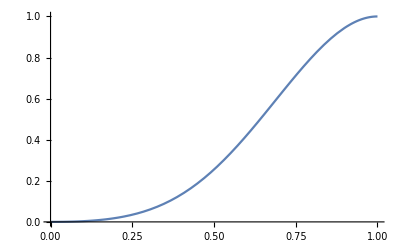

```mathematica
p1[p_]:=3 p^2-2 p^3

p2[p_] := 1-((1-p)^9+9*p*(1-p)^8)

pth[p_]=p1[p]^2/p2[p]

pth[0.001] 

Plot[pth[p],{p,0,1}]
```